# Mellin transform

```mathematica
ResumConst={CF-> 4/3,CA-> 3,nf->5,nl->nf-1,Tf-> 1/2,β0f-> (11 CA- 2 nf)/(12π),β0l-> (11 CA- 2 nl)/(12π),β1f-> (17 CA^2 - 5 CA nf- 3 CF nf)/(24 π^2),β1l-> (17 CA^2 - 5 CA nl- 3 CF nl)/(24 π^2),Kf->CA (67/18-π^2/6)-5/9 nf,Kl->CA (67/18-π^2/6)-5/9 nl, A1->CF, A2f->1/2 CF Kf,A2l->1/2 CF Kl, B1-> -3/2 CF,
H1-> -CF,s1-> -CF};
```

## Definition of the functions

```mathematica
f1[λ_,z_]= Log[1-λ z]/(1-z);
f2[λ_,z_]= 1/(1-λ z);
f3[λ_,z_]= (1-z)/(1-λ z)^2;
```

## Mellin transform with Catani expressions

First function

```mathematica
M1[Nb_,λ_]:= -NIntegrate[f1[λ,z],{z,0,1-1/Nb}]
```

```mathematica
M1analytics[Nb_,λ_]:= PolyLog[2,-λ/(1-λ)]-PolyLog[2,-λ/(Nb(1-λ))]-Log[Nb]Log[(1-λ)/λ]-Log[λ]Log[Nb]
```

Higher order terms

```mathematica
DM1[Nb_,λ_]= FullSimplify[D[M1analytics[Exp[u],λ],{u,2}]//.u-> Log[Nb]]
```

λ/(Nb+λ-Nb λ)

Second function

```mathematica
M2[Nb_,λ_]:= -NIntegrate[f2[λ,z],{z,0,1-1/Nb}]
```

```mathematica
FullSimplify[Assuming[Nb>1&&0<λ<1,Integrate[f2[λ,z],{z,0,1-1/Nb}]]]
```

-Log[1+(-1+1/Nb) λ]/λ

```mathematica
M2analytics[Nb_,λ_]:= 1/λ(Log[Nb(1-λ)+λ]-Log[Nb])
```

```mathematica
M2[100,0.6]/M2analytics[100,0.6]
```

1.

Third function

```mathematica
M3[Nb_,λ_]:= -NIntegrate[f3[λ,z],{z,0,1-1/Nb}]
```

```mathematica
FullSimplify[Assuming[Nb>1&&0<λ<1,Integrate[f3[λ,z],{z,0,1-1/Nb}]]]
```

-(-((-1+Nb) (-1+λ) λ)/(Nb+λ-Nb λ)+Log[1+(-1+1/Nb) λ])/λ^2

```mathematica
M3analytics[Nb_,λ_]:= 1/λ^2(Log[λ+Nb(1-λ)]-Log[Nb]+((Nb-1)(1-λ)λ)/(Nb(1-λ)+λ))
```

## Total Mellin transform

```mathematica
DISConst={α1-> 0, α2-> KA, α3->0,KA->((1-λ)Log[1-λ])/λ};
```

```mathematica
hq[Nb_,λ_]=-(4+1/(2λ)+π^2/3+(1+3λ)/(2λ)*((1-λ)Log[1-λ])/λ)+2(Log[Nb]^2+π^2/6-(M1analytics[Nb,λ]+Zeta[2]/2 DM1[Nb,λ]));
```

```mathematica
hq1[Nb_,λ_]= CF(hq[Nb,λ]+0+2Log[Nb]+1/(2 λ^2)(Log[(Nb(1-λ)+λ)/Nb]+(λ(1-λ)(Nb-1))/(Nb(1-λ)+λ)));
hq2[Nb_,λ_]= CF(hq[Nb,λ]+((1-λ)Log[1-λ])/λ+2Log[Nb]+1/(2 λ^2)(Log[(Nb(1-λ)+λ)/Nb]+(λ(1-λ)(Nb-1))/(Nb(1-λ)+λ)));
hq3[Nb_,λ_]= CF(hq[Nb,λ]+0+2Log[Nb]+1/(2 λ^2)(Log[(Nb(1-λ)+λ)/Nb]+(λ(1-λ)(Nb-1))/(Nb(1-λ)+λ)));
```

The result is multiplied by  α_S/(2π)

```mathematica
Hq1[Nb_,λ_,Q_,μf_]= 2CF(-Log[Nb]+3/4)Log[Q^2/(μf^2 λ)]+hq1[Nb,λ];
Hq2[Nb_,λ_,Q_,μf_]=2 CF(-Log[Nb]+3/4)Log[Q^2/(μf^2 λ)]+hq2[Nb,λ];
Hq3[Nb_,λ_,Q_,μf_]=2 CF(-Log[Nb]+3/4)Log[Q^2/(μf^2 λ)]+hq3[Nb,λ];
```

we consider small ξ and large Nb limit of hq1

```mathematica
Expand[FullSimplify[Normal[Series[hq1[Nb,λ]/CF//.Join[DISConst,{λ-> 1/(1+ξ)}],{Nb,Infinity,0},{ξ,0,0}]]]];
FunctionExpand[Assuming[ξ>0&&Nb>0,FullSimplify[Normal[Series[hq1[Nb,λ]/CF//.Join[DISConst,{λ-> 1/(1+ξ)}],{ξ,0,0},{Nb,Infinity,0}]]]]]
```

-9/2-π^2/6+(3 Log[Nb])/2+Log[Nb]^2

Expansion at large Nb with finite ξ

```mathematica
ExpHq1[Nb_,ξ_,Q_,μf_]=Expand[FullSimplify[Normal[Series[Hq1[Nb,λ,Q,μf]/(2CF)//.Join[DISConst,{λ-> 1/(1+ξ)}],{Nb,Infinity,0}]]]];
```

Resummation expansion at order α_S/π in the regime Nb ξ>1

```mathematica
Exp1[Nb_,ξ_,Q_,μf_]=1/CF(-A1 Log[Nb]Log[M2/μf^2]+A1 Log[Nb]^2-H1 (Log[Nb]+Log[ξ])+ A1 Log[ξ]Log[Q^2/M2]-1/2 A1 Log[ξ]^2+1/2 B1 Log[ξ])//.Join[{M2-> Q^2/ξ(1+ξ)^2},ResumConst];
```

```mathematica
Expand[Assuming[ξ>0&&Nb>0,FullSimplify[2*(ExpHq1[Nb,ξ,Q,μf]-Exp1[Nb,ξ,Q,μf])]]];
(*FullSimplify[%//.ξ-> (1-λ)/λ]*)
Expand[Assuming[ξ>0,Series[%,{ξ,0,0}]]]
```

1/6 (-24+2 π^2+9 Log[Q^2/μf^2])+O[ξ]^1

Expansion at large Nb with ξ=0

```mathematica
ExpHq2[Nb_,Q_,μf_]=Expand[Assuming[Nb>0&&ξ>0,FullSimplify[Normal[Series[Hq1[Nb,λ,Q,μf]/(2CF)//.Join[DISConst,{λ-> 1/(1+ξ)}],{ξ,0,0},{Nb,Infinity,0}]]]]]
```

-9/4-π^2/12+(3 Log[Nb])/4+Log[Nb]^2/2+3/4 Log[Q^2/μf^2]-Log[Nb] Log[Q^2/μf^2]

Resummation expansion at order α_S/π in the regime Nb ξ<1

```mathematica
Exp2[Nb_,Q_,μf_]=1/(2CF)(A1 Log[Nb]^2-B1 Log[Nb]-2A1 Log[Nb]Log[Q^2/μf^2])//.ResumConst;
```

```mathematica
Expand[Assuming[ξ>0&&Nb>0,FullSimplify[2*(ExpHq2[Nb,Q,μf]-Exp2[Nb,Q,μf])]]]
(*FullSimplify[%//.ξ-> (1-λ)/λ]*)
```

-9/2-π^2/6+3/2 Log[Q^2/μf^2]

## Subtracted functions

```mathematica
ResumExp[Nb_,ξ_,Q_,μf_]= Exp1[Nb,ξ,Q,μf]UnitStep[ξ-1/Nb]+Exp2[Nb,Q,μf]UnitStep[1/Nb- ξ];
```

I isolate a prefactor  α_S CF/(2π)

```mathematica
Hq1sub[Nb_,ξ_,Q_,μf_]= Hq1[Nb,1/(1+ξ),Q,μf]/CF-2*ResumExp[Nb,ξ,Q,μf];
Hq2sub[Nb_,ξ_,Q_,μf_]=Hq2[Nb,1/(1+ξ),Q,μf]/CF-2*ResumExp[Nb,ξ,Q,μf];
Hq3sub[Nb_,ξ_,Q_,μf_]=Hq3[Nb,1/(1+ξ),Q,μf]/CF-2*ResumExp[Nb,ξ,Q,μf];
```

```mathematica
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq1sub[Nb,ξ,Q,μf],{ξ,0,0},{Nb,Infinity,0}]]]
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq2sub[Nb,ξ,Q,μf],{ξ,0,0},{Nb,Infinity,0}]]]
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq3sub[Nb,ξ,Q,μf],{ξ,0,0},{Nb,Infinity,0}]]]
```

1/6 (-27-π^2+9 Log[Q^2/μf^2])+O[ξ]^1

1/6 (-27-π^2+9 Log[Q^2/μf^2])+O[ξ]^1

1/6 (-27-π^2+9 Log[Q^2/μf^2])+O[ξ]^1

```mathematica
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq1sub[Nb,ξ,Q,μf],{Nb,Infinity,0},{ξ,0,0}]]]
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq2sub[Nb,ξ,Q,μf],{Nb,Infinity,0},{ξ,0,0}]]]
Assuming[ξ>0&&Nb>0,FullSimplify[Series[Hq3sub[Nb,ξ,Q,μf],{Nb,Infinity,0},{ξ,0,0}]]]
```

((-4+π^2/3+3/2 Log[Q^2/μf^2])+O[ξ]^1)+O[1/Nb]^1

((-4+π^2/3+3/2 Log[Q^2/μf^2])+O[ξ]^1)+O[1/Nb]^1

((-4+π^2/3+3/2 Log[Q^2/μf^2])+O[ξ]^1)+O[1/Nb]^1

## Plots

Here I provide three sets of plots at different energies: Q=100 GeV, Q= 50 GeV, Q=20 GeV

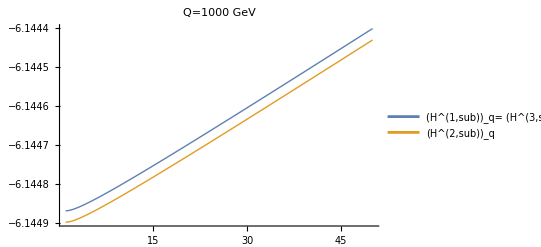

```mathematica
Plot[{Hq1sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 1000},ResumConst],Hq2sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 1000},ResumConst]},{Nb,1,50},PlotStyle->Thick,PlotLegends->{"(H^(1,sub))_q= (H^(3,sub))_q","(H^(2,sub))_q"},PlotLabel->"Q=1000 GeV"]
```

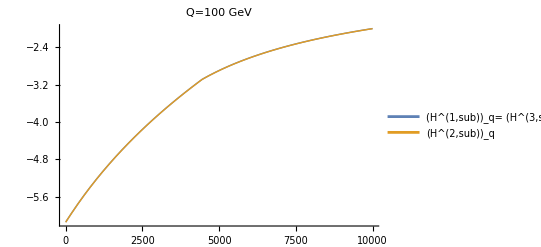

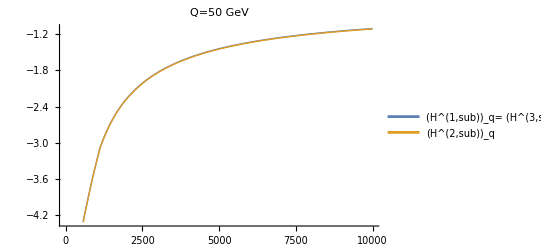

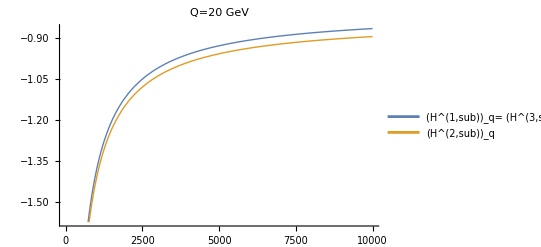

```mathematica
Plot[{Hq1sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 100},ResumConst],Hq2sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 100},ResumConst]},{Nb,1,10^4},PlotStyle->Thick,PlotLegends->{"(H^(1,sub))_q= (H^(3,sub))_q","(H^(2,sub))_q"},PlotLabel->"Q=100 GeV"]
Plot[{Hq1sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 50},ResumConst],Hq2sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 50},ResumConst]},{Nb,1,10^4},PlotStyle->Thick,PlotLegends->{"(H^(1,sub))_q= (H^(3,sub))_q","(H^(2,sub))_q"},PlotLabel->"Q=50 GeV"]
Plot[{Hq1sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 20},ResumConst],Hq2sub[Nb,m^2/Q^2,Q,Q]//.Join[{m->1.5, Q-> 20},ResumConst]},{Nb,1,10^4},PlotStyle->Thick,PlotLegends->{"(H^(1,sub))_q= (H^(3,sub))_q","(H^(2,sub))_q"},PlotLabel->"Q=20 GeV"]
```

```mathematica
N[-4+π^2/3]
```

-0.710132